Basic analysis of dumps captured from Android battery  ”uevent” fuel gauge interface

Phillip Stanley-Marbell
phillip.stanleymarbell@gmail.com / psm@mit.edu

March 2016

```mathematica
SetDirectory[NotebookDirectory[]];

analyze[deviceFamily_, fileName_, dateRange_] := Module[{grepCurrentBeforeCount,grepVoltageBeforeCount, currentGroupSize, voltageGroupSize,currentIndex,voltageIndex,
rawCurrents,rawVoltages,rawCurrentsGrouped,rawVoltagesGrouped,datesAndCurrentsMicroamps,datesAndDischargeCurrentsMicroamps,datesAndDischargeCurrentsAbsoluteMicroamps,datesAndVoltageMicrovolts, datesAndPowerMilliwatts, averagePowerMilliwatts,datesAndDischargeCurrentsAbsoluteMicroampsSubset,datesAndVoltageMicrovoltsSubset,minPowerMilliwatts},

grepCurrentBeforeCount = Switch[deviceFamily,
"nexus6p",15,
"max17047_battery", 11,
_,11];

grepVoltageBeforeCount = Switch[deviceFamily ,
 "nexus6p",17,
"max17047_battery",6,
	_,9];

currentGroupSize = grepCurrentBeforeCount+2;

voltageGroupSize =grepVoltageBeforeCount + 2;

currentIndex = Switch[deviceFamily ,
"nexus6p",16,
"max17047_battery",12,
	_,12];

voltageIndex = Switch[deviceFamily ,
 "nexus6p",18,
"max17047_battery",7,
_,10];



rawCurrents =Import["!grep -B "<>ToString[grepCurrentBeforeCount]<>" 'POWER_SUPPLY_CURRENT_NOW' "<>fileName, "List"];
(*Print["rawCurrents: ", rawCurrents];*)

rawCurrentsGrouped = Partition[rawCurrents, currentGroupSize];
(*Print["rawCurrentsGrouped: ", rawCurrentsGrouped];*)

datesAndCurrentsMicroamps= {DateObject[#[[1]]], ToExpression[StringSplit[#[[currentIndex]], "="][[2]]]}&/@rawCurrentsGrouped;
datesAndDischargeCurrentsMicroamps = {#[[1]], Abs[#[[2]]]}&/@datesAndCurrentsMicroamps;(*Select[datesAndCurrentsMicroamps, #[[2]]≤ 0&];*)
datesAndDischargeCurrentsAbsoluteMicroamps = {#[[1]], Abs[#[[2]]]/10^3}&/@ datesAndDischargeCurrentsMicroamps;
(*Print["datesAndDischargeCurrentsAbsoluteMicroamps: ", datesAndDischargeCurrentsAbsoluteMicroamps];*)

datesAndDischargeCurrentsAbsoluteMicroampsSubset = Select[datesAndDischargeCurrentsAbsoluteMicroamps, (DateDifference[#[[1]], dateRange[[1]], "Second"]< Quantity[0, "Second"] && DateDifference[#[[1]], dateRange[[2]], "Second"]> Quantity[0, "Second"])&];

(*Print["datesAndDischargeCurrentsAbsoluteMicroampsSubset: ", datesAndDischargeCurrentsAbsoluteMicroampsSubset];*)



rawVoltages =Import["!grep -B "<>ToString[grepVoltageBeforeCount]<>" 'POWER_SUPPLY_VOLTAGE_NOW' "<>fileName, "List"];
rawVoltagesGrouped = Partition[rawVoltages, voltageGroupSize];
datesAndVoltageMicrovolts= {DateObject[#[[1]]], ToExpression[StringSplit[#[[voltageIndex]], "="][[2]]]/10^6}&/@rawVoltagesGrouped;

datesAndVoltageMicrovoltsSubset = Select[datesAndVoltageMicrovolts, (DateDifference[#[[1]], dateRange[[1]], "Second"]< Quantity[0, "Second"] && DateDifference[#[[1]], dateRange[[2]], "Second"]> Quantity[0, "Second"])&];
(*Print["datesAndVoltageMicrovoltsSubset: ", datesAndVoltageMicrovoltsSubset];*)




datesAndPowerMilliwatts = Table[{datesAndDischargeCurrentsAbsoluteMicroampsSubset[[i]][[1]], datesAndDischargeCurrentsAbsoluteMicroampsSubset[[i]][[2]]*datesAndVoltageMicrovoltsSubset[[i]][[2]]}, {i, 1, Length[datesAndDischargeCurrentsAbsoluteMicroampsSubset]}];

averagePowerMilliwatts = NumberForm[N[Mean[Table[datesAndDischargeCurrentsAbsoluteMicroampsSubset[[i]][[2]]*datesAndVoltageMicrovoltsSubset[[i]][[2]], {i, 1, Length[datesAndDischargeCurrentsAbsoluteMicroampsSubset]}]]], {3,2}];

minPowerMilliwatts = NumberForm[N[Min[Table[datesAndDischargeCurrentsAbsoluteMicroampsSubset[[i]][[2]]*datesAndVoltageMicrovoltsSubset[[i]][[2]], {i, 1, Length[datesAndDischargeCurrentsAbsoluteMicroampsSubset]}]]], {3,2}];

{Column[{DateListPlot[datesAndDischargeCurrentsAbsoluteMicroampsSubset,
AspectRatio->1/3,
PlotRange-> {dateRange, Automatic},
PlotTheme->"Detailed",
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Sampled Battery Current (mA)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}],
DateListLogPlot[datesAndDischargeCurrentsAbsoluteMicroampsSubset,
AspectRatio->1/3,
PlotTheme->"Detailed",
PlotRange-> {dateRange, Automatic},
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Sampled Battery Current (mA)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}],


DateListPlot[datesAndVoltageMicrovoltsSubset,
AspectRatio->1/3,
PlotRange-> {dateRange, {0, 4.6}},
PlotTheme->"Detailed",
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Sampled Battery Voltage (Volts)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}],

DateListLogPlot[datesAndVoltageMicrovoltsSubset,
AspectRatio->1/3,
PlotRange-> {dateRange, {0.1, 10}},
PlotTheme->"Detailed",
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Sampled Battery Voltage (Volts)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}],


DateListPlot[datesAndPowerMilliwatts,
AspectRatio->1/3,
PlotTheme->"Detailed",
PlotRange-> {dateRange, Automatic},
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Power Drain (mW)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}},
Epilog-> Inset[Style["Average power drain = "<>ToString[averagePowerMilliwatts]<>" mW, "<>"Min power drain = "<>ToString[minPowerMilliwatts]<>" mW,\n",FontFamily-> "Helvetica Neue",FontSize-> 16, Background-> Directive[LightBlue, Opacity[0.5]]], Scaled[{0.5, 0.90}]]],

DateListLogPlot[datesAndPowerMilliwatts,
AspectRatio->1/3,
PlotTheme->"Detailed",
PlotRange-> {dateRange, Automatic},
ImageSize->800,
Frame->True,
InterpolationOrder->0,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Power Drain (mW)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}},
Epilog-> Inset[Style["Average power drain = "<>ToString[averagePowerMilliwatts]<>" mW,  "<>"Min power drain = "<>ToString[minPowerMilliwatts]<>" mW",FontFamily-> "Helvetica Neue",FontSize-> 16, Background-> Directive[LightBlue, Opacity[0.5]]], Scaled[{0.5, 0.90}]]
]
}
],({#[[1]], N[#[[2]]]}&/@ datesAndPowerMilliwatts)//TableForm}];
```

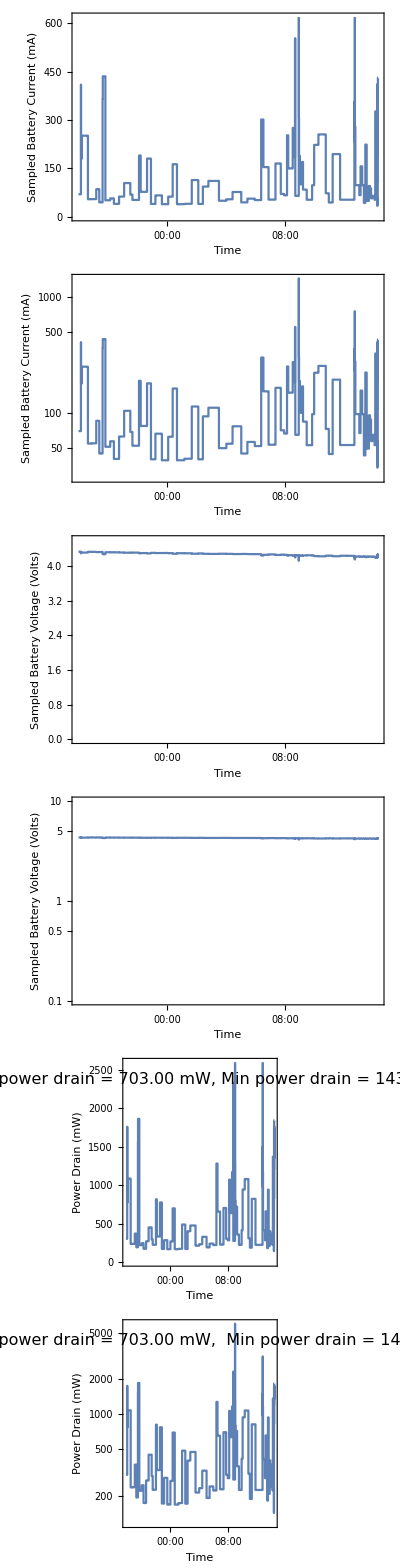
{-Graphics-,1}
 |  |  |  |

```mathematica
analyze["nexus6p", "../Logs/2016-02-03-14-15-47.txt",{{2016,2,2, 18,0},{2016,2,3, 14, 15}}]
```